## Figure 4 (Asymmetry in conditioning ability and niche width)

### Setup

```mathematica
f[a_,b_,p_,q_]:= NIntegrate[Exp[(-(x-p)^2)/a^2]Exp[(-(x-q)^4)/(81 b^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[(-(x-p)^2)/a^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]=Subscript[N, 1](1-S^4/Subscript[ω, 1]^4-(Subscript[N, 1]+Subscript[ν, 1] Subscript[α, 12]  Subscript[N, 2]));
Subscript[dN, 2]=Subscript[N, 2](1-(S-ϵ)^4/Subscript[ω, 2]^4-(Subscript[ν, 2] Subscript[α, 21] Subscript[N, 1]+Subscript[N, 2]));
dS=Subscript[η, 1](-S)Subscript[N, 1]+Subscript[η, 2](ϵ-S)Subscript[N, 2];
```

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

### Symmetric case for reference

#### Calculation

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,6]
```

0.000785406

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]];

If[(Length[eq[[j1,j2]]]==2||Length[eq[[j1,j2]]]>3),Print[{ζs[[j1]],ϵs[[j2]],Length[eq[[j1,j2]]]}]];

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{71.3125,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

#### Result

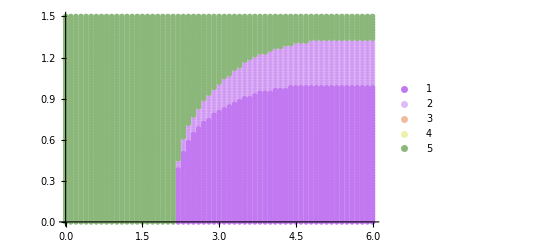

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

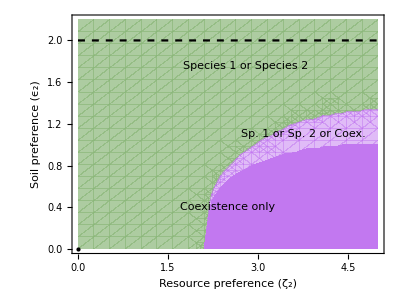

```mathematica
Show[{RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,5},{y,0,2.2},PlotStyle->{{ColorData[95,0],Opacity[0.7]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None],Plot[(Subscript[ω, 1]+Subscript[ω, 2])/.pars,{ζ,0,5},PlotStyle->{Dashed,Black}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{2.8,1.75}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{3.75,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{2.5,0.4}]}},AspectRatio->0.75]
```

```mathematica
z1Sym=z1;
z2Sym=z2;
```

### Figure 4a (Asymmetry in η)

#### Mild asymmetery η_1=1, η_2=1.2

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1.2};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[1.5,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]];

If[(Length[eq[[j1,j2]]]==2||Length[eq[[j1,j2]]]>3),Print[{ζs[[j1]],ϵs[[j2]],Length[eq[[j1,j2]]]}]];

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Max::nord: Invalid comparison with -0.993832-0.0018861 ⅈ attempted.

Max::nord: Invalid comparison with -0.993832+0.0018861 ⅈ attempted.

Less::nord2: Comparison of Max[-0.993832-0.0018861 ⅈ,-0.993832+0.0018861 ⅈ,0.123334+0. ⅈ] and 0 is invalid.

GreaterEqual::nord2: Comparison of Max[-0.993832-0.0018861 ⅈ,-0.993832+0.0018861 ⅈ,0.123334+0. ⅈ] and 0 is invalid.

General::stop: Further output of GreaterEqual::nord2 will be suppressed during this calculation.

Max::nord: Invalid comparison with -0.994304-0.00268021 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Less::nord2: Comparison of Max[-0.994304-0.00268021 ⅈ,-0.994304+0.00268021 ⅈ,0.125868+0. ⅈ] and 0 is invalid.

General::stop: Further output of Less::nord2 will be suppressed during this calculation.

{54.4844,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

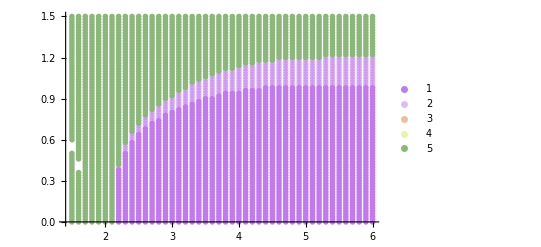

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

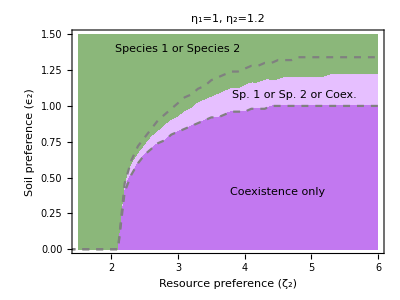

```mathematica
fig4a1=Show[{RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,1.5,6},{y,0,1.5},PlotStyle->{{ColorData[95,0],Opacity[1]},{RGBColor[0.9,0.75,1,0.99]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None],ListLinePlot[{z1Sym,z2Sym},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["η_1=1, η_2=1.2",FontSize->18],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->18,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{3,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->15]],{4.75,1.075}],Inset[Text[Style["Coexistence only ",FontSize->15]],{4.5,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4a.pdf",fig4a1];
```

```mathematica
z1a=z1;
z2a=z2;
```

#### Intermediate asymmetery η_1=1, η_2=1.5

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1.5};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[1.5,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]];

If[(Length[eq[[j1,j2]]]==2||Length[eq[[j1,j2]]]>3),Print[{ζs[[j1]],ϵs[[j2]],Length[eq[[j1,j2]]]}]];

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{54.7188,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

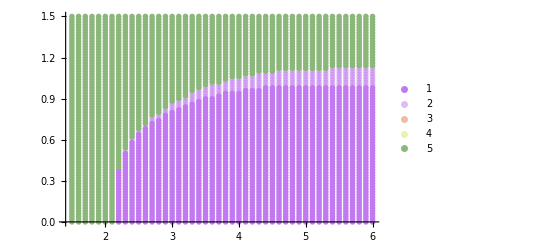

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

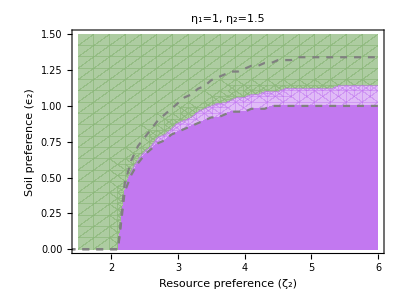

```mathematica
fig4a2=Show[{RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,1.5,6},{y,0,1.5},PlotStyle->{{ColorData[95,0],Opacity[0.7]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None],ListLinePlot[{z1Sym,z2Sym},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["η_1=1, η_2=1.5",FontSize->18],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->18,FontColor->Black},AspectRatio->0.75]
```

#### Strong asymmetery η_1=1, η_2=2

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->2};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[1.5,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]];

If[(Length[eq[[j1,j2]]]==2||Length[eq[[j1,j2]]]>3),Print[{ζs[[j1]],ϵs[[j2]],Length[eq[[j1,j2]]]}]];

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{55.6094,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

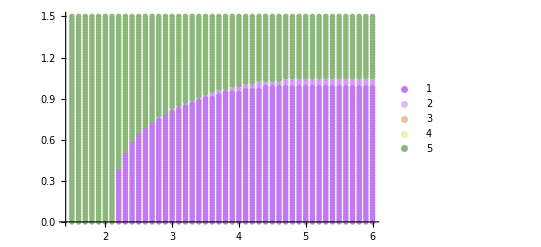

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

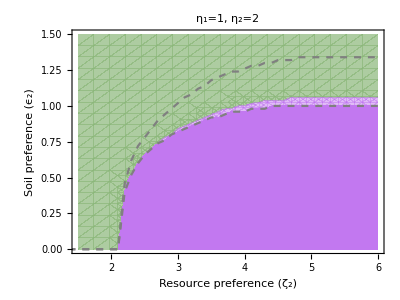

```mathematica
fig4a3=Show[{RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,1.5,6},{y,0,1.5},PlotStyle->{{ColorData[95,0],Opacity[0.7]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None],ListLinePlot[{z1Sym,z2Sym},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["η_1=1, η_2=2",FontSize->18],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->18,FontColor->Black},AspectRatio->0.75]
```

#### Summary

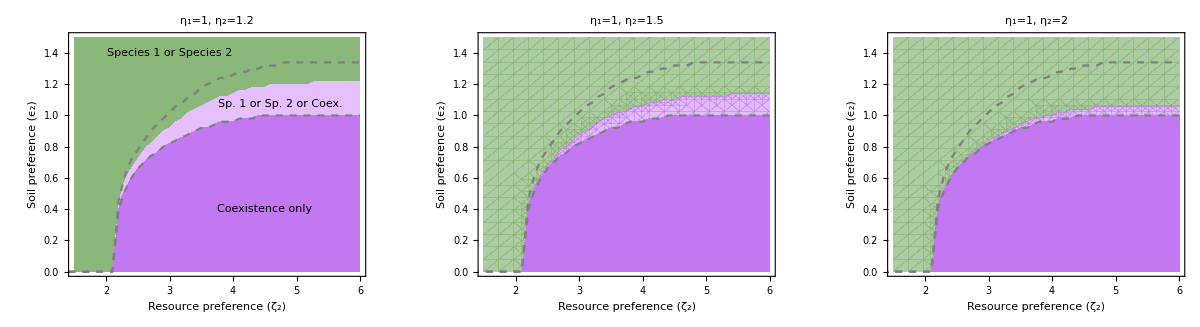

```mathematica
GraphicsRow[{fig4a1,fig4a2,fig4a3},ImageSize->1200]
```

### Figure 4b (Asymmetry in ω)

#### Mild asymmtery ω_1=1, ω_2=1.1

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1.1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[1.5,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]];
If[Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]<0,Print[{j1,j2,eq[[j1,j2]],Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]}]]]];

If[Length[eq[[j1,j2]]]==1,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}];
If[Im[λ[[1]]]!=0,Print[{2,ζs[[j1]],ϵs[[j2]]}],
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}];
If[Im[λ[[1]]]!=0,Print[{3,ζs[[j1]],ϵs[[j2]]}],
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ3[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ1[[j1,j2]]<0&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{1,1.5,0.88}

{1,1.5,0.9}

{1,1.6,0.84}

{1,1.6,0.86}

{1,1.6,0.88}

{1,1.7,0.8}

{1,1.7,0.82}

{1,1.7,0.84}

{1,1.8,0.76}

{1,1.8,0.78}

{1,1.8,0.8}

{1,1.9,0.7}

{1,1.9,0.72}

{1,1.9,0.74}

{1,2.,0.62}

{1,2.,0.64}

{1,2.1,0.48}

{1,2.1,0.5}

{59.6719,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{0,3037,176,283,0,0}

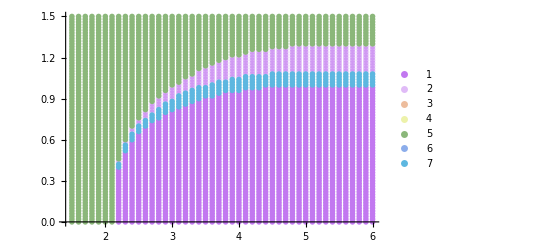

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[Drop[z2,7]];
f3=Interpolation[z3];
```

```mathematica
z2
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{Null[5,1],Null[5,2]},{Null[6,1],Null[6,2]},{Null[7,1],Null[7,2]},{2.2,0.44},{2.3,0.58},{2.4,0.66},{2.5,0.72},{2.6,0.76},{2.7,0.8},{2.8,0.84},{2.9,0.88},{3.,0.9},{3.1,0.94},{3.2,0.96},{3.3,0.98},{3.4,1.},{3.5,1.},{3.6,1.02},{3.7,1.04},{3.8,1.04},{3.9,1.06},{4.,1.06},{4.1,1.08},{4.2,1.08},{4.3,1.08},{4.4,1.08},{4.5,1.1},{4.6,1.1},{4.7,1.1},{4.8,1.1},{4.9,1.1},{5.,1.1},{5.1,1.1},{5.2,1.1},{5.3,1.1},{5.4,1.1},{5.5,1.1},{5.6,1.1},{5.7,1.1},{5.8,1.1},{5.9,1.1},{6.,1.1}}

InterpolatingFunction::dmval: Input value {1.50024} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.09211} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

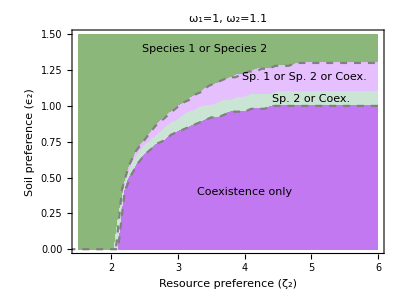

```mathematica
fig4b1=Show[{RegionPlot[{y>f3[x],y<f3[x],y<f1[x]},{x,1.5,6},{y,0,1.5},PlotStyle->{{ColorData[95,0],Opacity[1]},{RGBColor[0.9,0.75,1,0.99]}},BoundaryStyle->None],RegionPlot[{y<f2[x],y<f1[x]},{x,1.5,6},{y,0,1.5},PlotStyle->{{ColorData["Pastel",0.8],Opacity[1]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None],ListLinePlot[{z1Sym,z2Sym-0.04},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["ω_1=1, ω_2=1.1",FontSize->18],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->18,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{3.4,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->15]],{4.9,1.2}],Inset[Text[Style["Sp. 2 or Coex. ",FontSize->15]],{5,1.05}],Inset[Text[Style["Coexistence only ",FontSize->15]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4b1.pdf",fig4b1];
```

```mathematica
z1b=z1;
z2b=z2;
z3b=z3;
```

#### Intermediate asymmtery ω_1=1, ω_2=1.3

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1.3,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[1.5,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]];
If[Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]<0,Print[{j1,j2,eq[[j1,j2]],Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]}]]]];

If[Length[eq[[j1,j2]]]==1,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}];
If[Im[λ[[1]]]!=0,Print[{2,ζs[[j1]],ϵs[[j2]]}],
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}];
If[Im[λ[[1]]]!=0,Print[{3,ζs[[j1]],ϵs[[j2]]}],
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ3[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ1[[j1,j2]]<0&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{1,1.5,0.9}

{1,1.5,0.92}

{1,1.5,0.94}

{1,1.5,0.96}

{1,1.5,0.98}

{1,1.5,1.}

{1,1.5,1.02}

{1,1.5,1.04}

{1,1.6,0.86}

{1,1.6,0.88}

{1,1.6,0.9}

{1,1.6,0.92}

{1,1.6,0.94}

{1,1.6,0.96}

{1,1.6,0.98}

{1,1.6,1.}

{1,1.7,0.82}

{1,1.7,0.84}

{1,1.7,0.86}

{1,1.7,0.88}

{1,1.7,0.9}

{1,1.7,0.92}

{1,1.7,0.94}

{1,1.7,0.96}

{1,1.8,0.78}

{1,1.8,0.8}

{1,1.8,0.82}

{1,1.8,0.84}

{1,1.8,0.86}

{1,1.8,0.88}

{1,1.8,0.9}

{1,1.9,0.72}

{1,1.9,0.74}

{1,1.9,0.76}

{1,1.9,0.78}

{1,1.9,0.8}

{1,1.9,0.82}

{1,1.9,0.84}

{1,2.,0.64}

{1,2.,0.66}

{1,2.,0.68}

{1,2.,0.7}

{1,2.,0.72}

{1,2.,0.74}

{1,2.1,0.5}

{1,2.1,0.52}

{1,2.1,0.54}

{1,2.1,0.56}

{60.6406,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{87,2973,436,0,0,0}

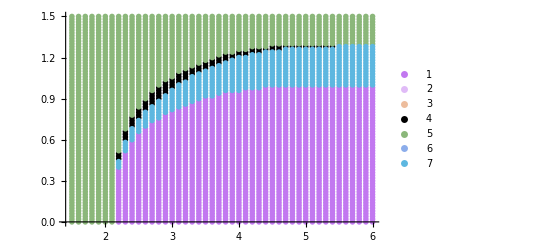

```mathematica
fig4b21=ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},Black,{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

#### Strong asymmtery ω_1=1, ω_2=1.4

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1.4,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[1.5,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]];
If[Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]<0,Print[{j1,j2,eq[[j1,j2]],Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]}]]]];

If[Length[eq[[j1,j2]]]==1,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}];
If[Im[λ[[1]]]!=0,Print[{2,ζs[[j1]],ϵs[[j2]]}],
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}];
If[Im[λ[[1]]]!=0,Print[{3,ζs[[j1]],ϵs[[j2]]}],
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]]];
eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ3[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]>=0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{1,1.5,0.9}

{1,1.5,0.92}

{1,1.5,0.94}

{1,1.5,0.96}

{1,1.5,0.98}

{1,1.5,1.}

{1,1.5,1.02}

{1,1.5,1.04}

{1,1.5,1.06}

{1,1.5,1.08}

{1,1.5,1.1}

{1,1.6,0.88}

{1,1.6,0.9}

{1,1.6,0.92}

{1,1.6,0.94}

{1,1.6,0.96}

{1,1.6,0.98}

{1,1.6,1.}

{1,1.6,1.02}

{1,1.6,1.04}

{1,1.6,1.06}

{1,1.7,0.84}

{1,1.7,0.86}

{1,1.7,0.88}

{1,1.7,0.9}

{1,1.7,0.92}

{1,1.7,0.94}

{1,1.7,0.96}

{1,1.7,0.98}

{1,1.7,1.}

{1,1.7,1.02}

{1,1.8,0.8}

{1,1.8,0.82}

{1,1.8,0.84}

{1,1.8,0.86}

{1,1.8,0.88}

{1,1.8,0.9}

{1,1.8,0.92}

{1,1.8,0.94}

{1,1.8,0.96}

{1,1.9,0.74}

{1,1.9,0.76}

{1,1.9,0.78}

{1,1.9,0.8}

{1,1.9,0.82}

{1,1.9,0.84}

{1,1.9,0.86}

{1,1.9,0.88}

{1,2.,0.66}

{1,2.,0.68}

{1,2.,0.7}

{1,2.,0.72}

{1,2.,0.74}

{1,2.,0.76}

{1,2.,0.78}

{1,2.1,0.5}

{1,2.1,0.52}

{1,2.1,0.54}

{1,2.1,0.56}

{1,2.1,0.58}

{1,2.1,0.6}

{55.8125,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{270,2796,430,0,0,0}

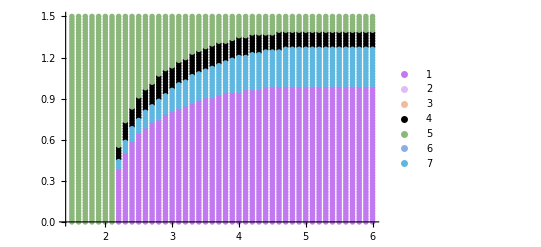

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},Black,{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[Drop[z2,7]];
f3=Interpolation[z3];
```

```mathematica
z2
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{Null[5,1],Null[5,2]},{Null[6,1],Null[6,2]},{Null[7,1],Null[7,2]},{2.2,0.46},{2.3,0.6},{2.4,0.7},{2.5,0.76},{2.6,0.82},{2.7,0.86},{2.8,0.9},{2.9,0.94},{3.,0.98},{3.1,1.02},{3.2,1.04},{3.3,1.08},{3.4,1.1},{3.5,1.12},{3.6,1.14},{3.7,1.16},{3.8,1.18},{3.9,1.2},{4.,1.22},{4.1,1.22},{4.2,1.24},{4.3,1.24},{4.4,1.26},{4.5,1.26},{4.6,1.26},{4.7,1.28},{4.8,1.28},{4.9,1.28},{5.,1.28},{5.1,1.28},{5.2,1.28},{5.3,1.28},{5.4,1.28},{5.5,1.28},{5.6,1.28},{5.7,1.28},{5.8,1.28},{5.9,1.28},{6.,1.28}}

InterpolatingFunction::dmval: Input value {2.10021} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.15132} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

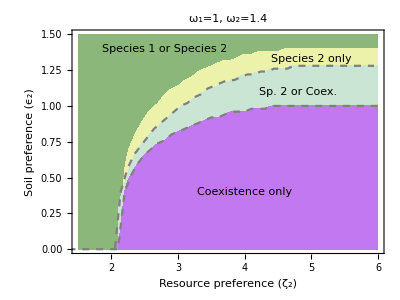

```mathematica
fig4b3=Show[{RegionPlot[{y>f3[x],y<f3[x]},{x,1.5,6},{y,0,1.5},PlotStyle->{{ColorData[95,0],Opacity[1]},{ColorData["Pastel",2/3],Opacity[1]}},BoundaryStyle->None],RegionPlot[{y<f2[x],y<f1[x]},{x,2.1,6},{y,0,1.5},PlotStyle->{{ColorData["Pastel",0.8],Opacity[1]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None],ListLinePlot[{z1Sym,z2Sym-0.06},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["ω_1=1, ω_2=1.4",FontSize->18],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->18,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{2.8,1.4}],Inset[Text[Style["Species 2 only ",FontSize->15]],{5,1.33}],Inset[Text[Style["Sp. 2 or Coex. ",FontSize->15]],{4.8,1.1}],Inset[Text[Style["Coexistence only ",FontSize->15]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4b2.pdf",fig4b3];
```

#### Summary

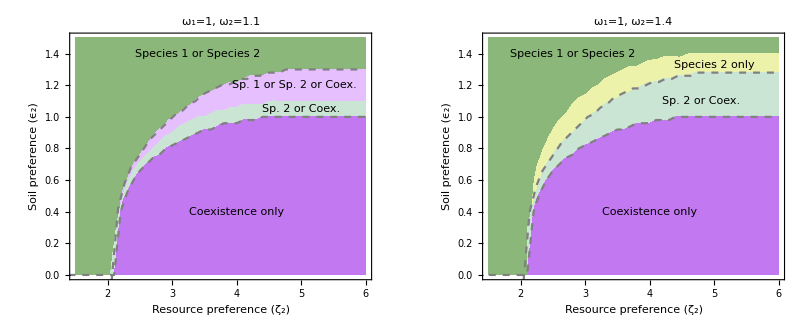

```mathematica
GraphicsRow[{fig4b1,fig4b3},ImageSize->800]
```

### Figure 4c (Asymmetry in σ)

#### Mild asymmtery σ_1=1, σ_2=1.2

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1.2,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[1.5,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch20=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]];
If[Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]<0,Print[{j1,j2,eq[[j1,j2]],Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]}]]]];

If[Length[eq[[j1,j2]]]==1,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}];
If[Im[λ[[1]]]!=0,Print[{2,ζs[[j1]],ϵs[[j2]]}],
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}];
If[Im[λ[[1]]]!=0,Print[{3,ζs[[j1]],ϵs[[j2]]}],
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ3[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ1[[j1,j2]]<0&&λ2[[j1,j2]]>0&&λ3[[j1,j2]]<0&&ch1==1&&ch20==0,ch20=1];
If[λ2[[j1,j2]]<0&&ch20==1&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]>0&&λ3[[j1,j2]]<0&&ch20==1&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,
If[λ2[[j1,j2-1]]<0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]},z4[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1];ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{1,1.5,0.8}

{1,1.5,0.82}

{1,1.5,0.84}

{1,1.5,0.86}

{1,1.5,0.88}

{1,1.5,0.9}

{1,1.5,0.92}

{1,1.6,0.78}

{1,1.6,0.8}

{1,1.6,0.82}

{1,1.6,0.84}

{1,1.6,0.86}

{1,1.6,0.88}

{1,1.6,0.9}

{1,1.6,0.92}

{1,1.7,0.72}

{1,1.7,0.74}

{1,1.7,0.76}

{1,1.7,0.78}

{1,1.7,0.8}

{1,1.7,0.82}

{1,1.7,0.84}

{1,1.7,0.86}

{1,1.7,0.88}

{1,1.7,0.9}

{1,1.8,0.68}

{1,1.8,0.7}

{1,1.8,0.72}

{1,1.8,0.74}

{1,1.8,0.76}

{1,1.8,0.78}

{1,1.8,0.8}

{1,1.8,0.82}

{1,1.8,0.84}

{1,1.8,0.86}

{1,1.8,0.88}

{1,1.8,0.9}

{1,1.9,0.62}

{1,1.9,0.64}

{1,1.9,0.66}

{1,1.9,0.68}

{1,1.9,0.7}

{1,1.9,0.72}

{1,1.9,0.74}

{1,1.9,0.76}

{1,1.9,0.78}

{1,1.9,0.8}

{1,1.9,0.82}

{1,1.9,0.84}

{1,1.9,0.86}

{1,1.9,0.88}

{1,2.,0.54}

{1,2.,0.56}

{1,2.,0.58}

{1,2.,0.6}

{1,2.,0.62}

{1,2.,0.64}

{1,2.,0.66}

{1,2.,0.68}

{1,2.,0.7}

{1,2.,0.72}

{1,2.,0.74}

{1,2.,0.76}

{1,2.,0.78}

{1,2.,0.8}

{1,2.,0.82}

{1,2.,0.84}

{1,2.,0.86}

{1,2.1,0.42}

{1,2.1,0.44}

{1,2.1,0.46}

{1,2.1,0.48}

{1,2.1,0.5}

{1,2.1,0.52}

{1,2.1,0.54}

{1,2.1,0.56}

{1,2.1,0.58}

{1,2.1,0.6}

{1,2.1,0.62}

{1,2.1,0.64}

{1,2.1,0.66}

{1,2.1,0.68}

{1,2.1,0.7}

{1,2.1,0.72}

{1,2.1,0.74}

{1,2.1,0.76}

{1,2.1,0.78}

{1,2.1,0.8}

{1,2.1,0.82}

{1,2.1,0.84}

{1,2.2,0.46}

{1,2.2,0.48}

{1,2.2,0.5}

{1,2.2,0.52}

{1,2.2,0.54}

{1,2.2,0.56}

{1,2.2,0.58}

{1,2.2,0.6}

{1,2.2,0.62}

{1,2.2,0.64}

{1,2.2,0.66}

{1,2.2,0.68}

{1,2.2,0.7}

{1,2.2,0.72}

{1,2.2,0.74}

{1,2.2,0.76}

{1,2.2,0.78}

{1,2.2,0.8}

{1,2.3,0.56}

{1,2.3,0.58}

{1,2.3,0.6}

{1,2.3,0.62}

{1,2.3,0.64}

{1,2.3,0.66}

{1,2.3,0.68}

{1,2.3,0.7}

{1,2.3,0.72}

{1,2.3,0.74}

{54.7813,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{231,2977,45,243,0,0}

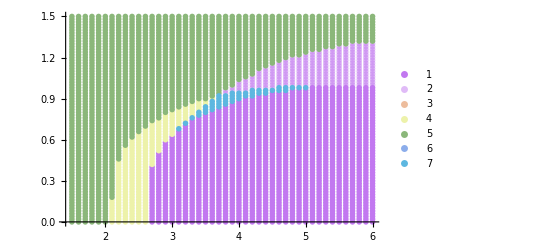

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[Take[z2,{17,36}]];
f3=Interpolation[Drop[z3,23]];
f4=Interpolation[Take[z4,{7,23}]];
```

```mathematica
z2
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{Null[5,1],Null[5,2]},{Null[6,1],Null[6,2]},{Null[7,1],Null[7,2]},{Null[8,1],Null[8,2]},{Null[9,1],Null[9,2]},{Null[10,1],Null[10,2]},{Null[11,1],Null[11,2]},{Null[12,1],Null[12,2]},{Null[13,1],Null[13,2]},{Null[14,1],Null[14,2]},{Null[15,1],Null[15,2]},{Null[16,1],Null[16,2]},{3.1,0.7},{3.2,0.74},{3.3,0.78},{3.4,0.82},{3.5,0.86},{3.6,0.9},{3.7,0.94},{3.8,0.94},{3.9,0.96},{4.,0.96},{4.1,0.96},{4.2,0.98},{4.3,0.98},{4.4,0.98},{4.5,0.98},{4.6,1.},{4.7,1.},{4.8,1.},{4.9,1.},{5.,1.},{Null[37,1],Null[37,2]},{Null[38,1],Null[38,2]},{Null[39,1],Null[39,2]},{Null[40,1],Null[40,2]},{Null[41,1],Null[41,2]},{Null[42,1],Null[42,2]},{Null[43,1],Null[43,2]},{Null[44,1],Null[44,2]},{Null[45,1],Null[45,2]},{Null[46,1],Null[46,2]}}

```mathematica
z3
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{Null[5,1],Null[5,2]},{Null[6,1],Null[6,2]},{Null[7,1],Null[7,2]},{Null[8,1],Null[8,2]},{Null[9,1],Null[9,2]},{Null[10,1],Null[10,2]},{Null[11,1],Null[11,2]},{Null[12,1],Null[12,2]},{Null[13,1],Null[13,2]},{Null[14,1],Null[14,2]},{Null[15,1],Null[15,2]},{Null[16,1],Null[16,2]},{Null[17,1],Null[17,2]},{Null[18,1],Null[18,2]},{Null[19,1],Null[19,2]},{Null[20,1],Null[20,2]},{Null[21,1],Null[21,2]},{Null[22,1],Null[22,2]},{Null[23,1],Null[23,2]},{3.8,0.98},{3.9,1.},{4.,1.04},{4.1,1.06},{4.2,1.08},{4.3,1.12},{4.4,1.14},{4.5,1.16},{4.6,1.18},{4.7,1.2},{4.8,1.22},{4.9,1.22},{5.,1.24},{5.1,1.26},{5.2,1.26},{5.3,1.28},{5.4,1.28},{5.5,1.3},{5.6,1.3},{5.7,1.32},{5.8,1.32},{5.9,1.32},{6.,1.32}}

```mathematica
z4
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{Null[5,1],Null[5,2]},{Null[6,1],Null[6,2]},{2.1,0.18},{2.2,0.46},{2.3,0.56},{2.4,0.62},{2.5,0.66},{2.6,0.7},{2.7,0.74},{2.8,0.76},{2.9,0.8},{3.,0.82},{3.1,0.84},{3.2,0.86},{3.3,0.88},{3.4,0.9},{3.5,0.9},{3.6,0.92},{3.7,0.94},{Null[24,1],Null[24,2]},{Null[25,1],Null[25,2]},{Null[26,1],Null[26,2]},{Null[27,1],Null[27,2]},{Null[28,1],Null[28,2]},{Null[29,1],Null[29,2]},{Null[30,1],Null[30,2]},{Null[31,1],Null[31,2]},{Null[32,1],Null[32,2]},{Null[33,1],Null[33,2]},{Null[34,1],Null[34,2]},{Null[35,1],Null[35,2]},{Null[36,1],Null[36,2]},{Null[37,1],Null[37,2]},{Null[38,1],Null[38,2]},{Null[39,1],Null[39,2]},{Null[40,1],Null[40,2]},{Null[41,1],Null[41,2]},{Null[42,1],Null[42,2]},{Null[43,1],Null[43,2]},{Null[44,1],Null[44,2]},{Null[45,1],Null[45,2]},{Null[46,1],Null[46,2]}}

InterpolatingFunction::dmval: Input value {1.50012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.75} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

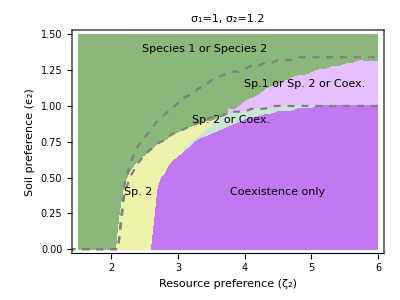

```mathematica
fig4c1=Show[{RegionPlot[{y<f4[x],y>f4[x]},{x,1.5,3.75},{y,0,1.5},PlotStyle->{{ColorData["Pastel",2/3],Opacity[1]},{ColorData[95,0]}},BoundaryStyle->None],RegionPlot[{y<f3[x]&&y>f1[x],y>f3[x]},{x,3.75,6},{y,0,1.5},PlotStyle->{{RGBColor[0.9,0.75,1,0.99]},{ColorData[95,0]}},BoundaryStyle->None],RegionPlot[y<f2[x],{x,3.1,5},{y,0,1.5},PlotStyle->{ColorData["Pastel",0.8],Opacity[1]},BoundaryStyle->None],RegionPlot[y<f1[x],{x,1.5,6},{y,0,1.5},PlotStyle->{ColorData["Pastel",0],Opacity[1]},BoundaryStyle->None],ListLinePlot[{z1Sym,z2Sym},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotRange->{{1.5,6},Automatic},PlotLabel->Style["σ_1=1, σ_2=1.2",FontSize->18],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->18,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{3.4,1.4}],Inset[Text[Style["Sp. 2",FontSize->15]],{2.4,0.4}],Inset[Text[Style["Sp. 2 or Coex.",FontSize->13]],{3.8,0.9}],Inset[Text[Style["Sp.1 or Sp. 2 or Coex. ",FontSize->15]],{4.9,1.15}],Inset[Text[Style["Coexistence only ",FontSize->15]],{4.5,0.4}]}},AspectRatio->0.75]
```

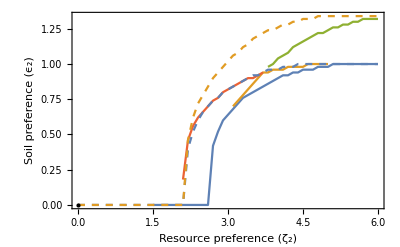

```mathematica
ListLinePlot[{z1,z2,z3,z4,z1Sym,z2Sym},PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3],ColorData[97,4],{ColorData[97,1],Dashed},{ColorData[97,2],Dashed}},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]}]
```

```mathematica
z1c=z1;
z2c=z2;
z3c=z3;
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4c.pdf",fig4c1];
```

#### Strong asymmtery σ_1=1, σ_2=1.5

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1.5,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[1.5,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch20=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]];
If[Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]<0,Print[{j1,j2,eq[[j1,j2]],Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]}]]]];

If[Length[eq[[j1,j2]]]==1,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}];
If[Im[λ[[1]]]!=0,Print[{2,ζs[[j1]],ϵs[[j2]]}],
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}];
If[Im[λ[[1]]]!=0,Print[{3,ζs[[j1]],ϵs[[j2]]}],
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ3[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ1[[j1,j2]]<0&&λ2[[j1,j2]]>0&&λ3[[j1,j2]]<0&&ch1==1&&ch20==0,ch20=1];
If[λ2[[j1,j2]]<0&&ch20==1&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]>0&&λ3[[j1,j2]]<0&&ch20==1&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,
If[λ2[[j1,j2-1]]<0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]},z4[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1];ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{1,1.5,0.74}

{1,1.5,0.76}

{1,1.5,0.78}

{1,1.5,0.8}

{1,1.5,0.82}

{1,1.5,0.84}

{1,1.5,0.86}

{1,1.5,0.88}

{1,1.5,0.9}

{1,1.5,0.92}

{1,1.5,0.94}

{1,1.5,0.96}

{1,1.5,0.98}

{1,1.6,0.7}

{1,1.6,0.72}

{1,1.6,0.74}

{1,1.6,0.76}

{1,1.6,0.78}

{1,1.6,0.8}

{1,1.6,0.82}

{1,1.6,0.84}

{1,1.6,0.86}

{1,1.6,0.88}

{1,1.6,0.9}

{1,1.6,0.92}

{1,1.6,0.94}

{1,1.6,0.96}

{1,1.6,0.98}

{1,1.7,0.66}

{1,1.7,0.68}

{1,1.7,0.7}

{1,1.7,0.72}

{1,1.7,0.74}

{1,1.7,0.76}

{1,1.7,0.78}

{1,1.7,0.8}

{1,1.7,0.82}

{1,1.7,0.84}

{1,1.7,0.86}

{1,1.7,0.88}

{1,1.7,0.9}

{1,1.7,0.92}

{1,1.7,0.94}

{1,1.7,0.96}

{1,1.7,0.98}

{1,1.8,0.6}

{1,1.8,0.62}

{1,1.8,0.64}

{1,1.8,0.66}

{1,1.8,0.68}

{1,1.8,0.7}

{1,1.8,0.72}

{1,1.8,0.74}

{1,1.8,0.76}

{1,1.8,0.78}

{1,1.8,0.8}

{1,1.8,0.82}

{1,1.8,0.84}

{1,1.8,0.86}

{1,1.8,0.88}

{1,1.8,0.9}

{1,1.8,0.92}

{1,1.8,0.94}

{1,1.8,0.96}

{1,1.8,0.98}

{1,1.9,0.56}

{1,1.9,0.58}

{1,1.9,0.6}

{1,1.9,0.62}

{1,1.9,0.64}

{1,1.9,0.66}

{1,1.9,0.68}

{1,1.9,0.7}

{1,1.9,0.72}

{1,1.9,0.74}

{1,1.9,0.76}

{1,1.9,0.78}

{1,1.9,0.8}

{1,1.9,0.82}

{1,1.9,0.84}

{1,1.9,0.86}

{1,1.9,0.88}

{1,1.9,0.9}

{1,1.9,0.92}

{1,1.9,0.94}

{1,1.9,0.96}

{1,1.9,0.98}

{1,2.,0.5}

{1,2.,0.52}

{1,2.,0.54}

{1,2.,0.56}

{1,2.,0.58}

{1,2.,0.6}

{1,2.,0.62}

{1,2.,0.64}

{1,2.,0.66}

{1,2.,0.68}

{1,2.,0.7}

{1,2.,0.72}

{1,2.,0.74}

{1,2.,0.76}

{1,2.,0.78}

{1,2.,0.8}

{1,2.,0.82}

{1,2.,0.84}

{1,2.,0.86}

{1,2.,0.88}

{1,2.,0.9}

{1,2.,0.92}

{1,2.,0.94}

{1,2.,0.96}

{1,2.1,0.44}

{1,2.1,0.46}

{1,2.1,0.48}

{1,2.1,0.5}

{1,2.1,0.52}

{1,2.1,0.54}

{1,2.1,0.56}

{1,2.1,0.58}

{1,2.1,0.6}

{1,2.1,0.62}

{1,2.1,0.64}

{1,2.1,0.66}

{1,2.1,0.68}

{1,2.1,0.7}

{1,2.1,0.72}

{1,2.1,0.74}

{1,2.1,0.76}

{1,2.1,0.78}

{1,2.1,0.8}

{1,2.1,0.82}

{1,2.1,0.84}

{1,2.1,0.86}

{1,2.1,0.88}

{1,2.1,0.9}

{1,2.1,0.92}

{1,2.1,0.94}

{1,2.1,0.96}

{1,2.2,0.54}

{1,2.2,0.56}

{1,2.2,0.58}

{1,2.2,0.6}

{1,2.2,0.62}

{1,2.2,0.64}

{1,2.2,0.66}

{1,2.2,0.68}

{1,2.2,0.7}

{1,2.2,0.72}

{1,2.2,0.74}

{1,2.2,0.76}

{1,2.2,0.78}

{1,2.2,0.8}

{1,2.2,0.82}

{1,2.2,0.84}

{1,2.2,0.86}

{1,2.2,0.88}

{1,2.2,0.9}

{1,2.2,0.92}

{1,2.2,0.94}

{1,2.2,0.96}

{1,2.3,0.6}

{1,2.3,0.62}

{1,2.3,0.64}

{1,2.3,0.66}

{1,2.3,0.68}

{1,2.3,0.7}

{1,2.3,0.72}

{1,2.3,0.74}

{1,2.3,0.76}

{1,2.3,0.78}

{1,2.3,0.8}

{1,2.3,0.82}

{1,2.3,0.84}

{1,2.3,0.86}

{1,2.3,0.88}

{1,2.3,0.9}

{1,2.3,0.92}

{1,2.3,0.94}

{1,2.4,0.64}

{1,2.4,0.66}

{1,2.4,0.68}

{1,2.4,0.7}

{1,2.4,0.72}

{1,2.4,0.74}

{1,2.4,0.76}

{1,2.4,0.78}

{1,2.4,0.8}

{1,2.4,0.82}

{1,2.4,0.84}

{1,2.4,0.86}

{1,2.4,0.88}

{1,2.4,0.9}

{1,2.4,0.92}

{1,2.4,0.94}

{1,2.5,0.68}

{1,2.5,0.7}

{1,2.5,0.72}

{1,2.5,0.74}

{1,2.5,0.76}

{1,2.5,0.78}

{1,2.5,0.8}

{1,2.5,0.82}

{1,2.5,0.84}

{1,2.5,0.86}

{1,2.5,0.88}

{1,2.5,0.9}

{1,2.6,0.7}

{1,2.6,0.72}

{1,2.6,0.74}

{1,2.6,0.76}

{1,2.6,0.78}

{1,2.6,0.8}

{1,2.6,0.82}

{1,2.6,0.84}

{1,2.6,0.86}

{54.2031,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{621,2755,49,71,0,0}

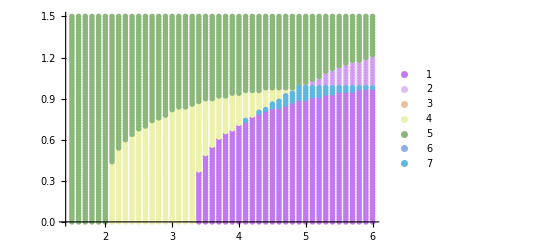

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[Drop[z2,28]];
f3=Interpolation[Drop[z3,36]];
f4=Interpolation[Take[z4,{7,35}]];
```

```mathematica
z2
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{Null[5,1],Null[5,2]},{Null[6,1],Null[6,2]},{Null[7,1],Null[7,2]},{Null[8,1],Null[8,2]},{Null[9,1],Null[9,2]},{Null[10,1],Null[10,2]},{Null[11,1],Null[11,2]},{Null[12,1],Null[12,2]},{Null[13,1],Null[13,2]},{Null[14,1],Null[14,2]},{Null[15,1],Null[15,2]},{Null[16,1],Null[16,2]},{Null[17,1],Null[17,2]},{Null[18,1],Null[18,2]},{Null[19,1],Null[19,2]},{Null[20,1],Null[20,2]},{Null[21,1],Null[21,2]},{Null[22,1],Null[22,2]},{Null[23,1],Null[23,2]},{Null[24,1],Null[24,2]},{Null[25,1],Null[25,2]},{Null[26,1],Null[26,2]},{4.1,0.76},{Null[28,1],Null[28,2]},{4.3,0.82},{4.4,0.84},{4.5,0.88},{4.6,0.9},{4.7,0.94},{4.8,0.96},{4.9,1.},{5.,1.},{5.1,1.},{5.2,1.},{5.3,1.},{5.4,1.},{5.5,1.},{5.6,1.},{5.7,1.},{5.8,1.},{5.9,1.},{6.,1.}}

```mathematica
z3
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{Null[5,1],Null[5,2]},{Null[6,1],Null[6,2]},{Null[7,1],Null[7,2]},{Null[8,1],Null[8,2]},{Null[9,1],Null[9,2]},{Null[10,1],Null[10,2]},{Null[11,1],Null[11,2]},{Null[12,1],Null[12,2]},{Null[13,1],Null[13,2]},{Null[14,1],Null[14,2]},{Null[15,1],Null[15,2]},{Null[16,1],Null[16,2]},{Null[17,1],Null[17,2]},{Null[18,1],Null[18,2]},{Null[19,1],Null[19,2]},{Null[20,1],Null[20,2]},{Null[21,1],Null[21,2]},{Null[22,1],Null[22,2]},{Null[23,1],Null[23,2]},{Null[24,1],Null[24,2]},{Null[25,1],Null[25,2]},{Null[26,1],Null[26,2]},{Null[27,1],Null[27,2]},{Null[28,1],Null[28,2]},{Null[29,1],Null[29,2]},{Null[30,1],Null[30,2]},{Null[31,1],Null[31,2]},{Null[32,1],Null[32,2]},{Null[33,1],Null[33,2]},{Null[34,1],Null[34,2]},{Null[35,1],Null[35,2]},{5.,1.02},{5.1,1.04},{5.2,1.06},{5.3,1.1},{5.4,1.12},{5.5,1.14},{5.6,1.16},{5.7,1.18},{5.8,1.18},{5.9,1.2},{6.,1.22}}

```mathematica
z4
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{Null[5,1],Null[5,2]},{Null[6,1],Null[6,2]},{2.1,0.44},{2.2,0.54},{2.3,0.6},{2.4,0.64},{2.5,0.68},{2.6,0.7},{2.7,0.74},{2.8,0.76},{2.9,0.78},{3.,0.82},{3.1,0.84},{3.2,0.84},{3.3,0.86},{3.4,0.88},{3.5,0.9},{3.6,0.9},{3.7,0.92},{3.8,0.92},{3.9,0.94},{4.,0.94},{4.1,0.96},{4.2,0.96},{4.3,0.96},{4.4,0.98},{4.5,0.98},{4.6,0.98},{4.7,0.98},{4.8,0.98},{4.9,1.},{Null[36,1],Null[36,2]},{Null[37,1],Null[37,2]},{Null[38,1],Null[38,2]},{Null[39,1],Null[39,2]},{Null[40,1],Null[40,2]},{Null[41,1],Null[41,2]},{Null[42,1],Null[42,2]},{Null[43,1],Null[43,2]},{Null[44,1],Null[44,2]},{Null[45,1],Null[45,2]},{Null[46,1],Null[46,2]}}

InterpolatingFunction::dmval: Input value {1.50018} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

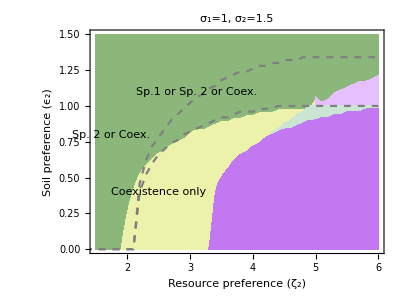

```mathematica
fig4c2=Show[{RegionPlot[{y<f4[x],y>f4[x]},{x,1.5,5},{y,0,1.5},PlotStyle->{{ColorData["Pastel",2/3],Opacity[1]},{ColorData[95,0],Opacity[1]}},BoundaryStyle->None],RegionPlot[{y<f3[x]&&y>f1[x],y>f3[x]},{x,5,6},{y,0,1.5},PlotStyle->{{RGBColor[0.9,0.75,1,0.99]},{ColorData[95,0],Opacity[1]}},BoundaryStyle->None],RegionPlot[y<f2[x],{x,4.3,6},{y,0,1.5},PlotStyle->{ColorData["Pastel",0.8],Opacity[1]},BoundaryStyle->None],RegionPlot[y<f1[x],{x,1.5,6},{y,0,1.5},PlotStyle->{ColorData["Pastel",0],Opacity[1]},BoundaryStyle->None],ListLinePlot[{z1Sym,z2Sym},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotRange->{{1.5,6},Automatic},PlotLabel->Style["σ_1=1, σ_2=1.5",FontSize->18],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->18,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{1.4,1.4}],Inset[Text[Style["Sp. 2",FontSize->15]],{0.4,0.4}],Inset[Text[Style["Sp. 2 or Coex.",FontSize->13]],{1.75,0.8}],Inset[Text[Style["Sp.1 or Sp. 2 or Coex. ",FontSize->15]],{3.1,1.1}],Inset[Text[Style["Coexistence only ",FontSize->15]],{2.5,0.4}]}},AspectRatio->0.75]
```

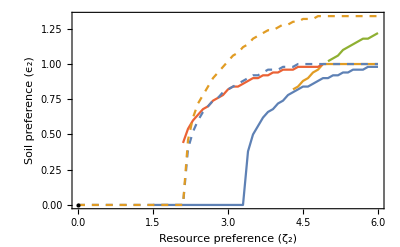

```mathematica
ListLinePlot[{z1,z2,z3,z4,z1Sym,z2Sym},PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3],ColorData[97,4],{ColorData[97,1],Dashed},{ColorData[97,2],Dashed}},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]}]
```

#### Summary

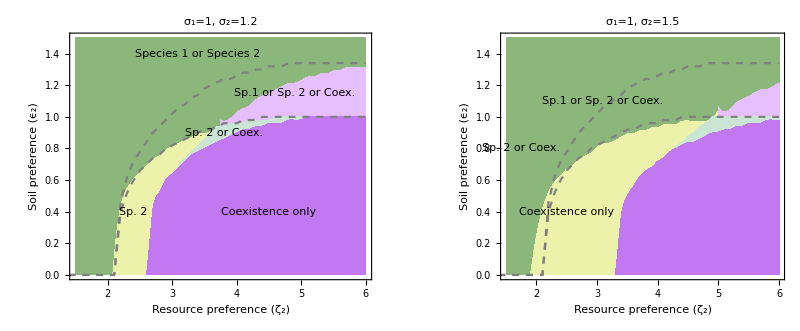

```mathematica
GraphicsRow[{fig4c1,fig4c2},ImageSize->800]
```

### Figure 4d (Asymmetry in ν)

#### Mild asymmety ν_1=1, ν_2=0.9

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->0.9,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[1.5,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch20=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]];
If[Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]<0,Print[{j1,j2,eq[[j1,j2]],Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]}]]]];

If[Length[eq[[j1,j2]]]==1,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}];
If[Im[λ[[1]]]!=0,Print[{2,ζs[[j1]],ϵs[[j2]]}],
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}];
If[Im[λ[[1]]]!=0,Print[{3,ζs[[j1]],ϵs[[j2]]}],
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ3[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ1[[j1,j2]]<0&&λ2[[j1,j2]]>0&&λ3[[j1,j2]]<0&&ch1==1&&ch20==0,ch20=1];
If[λ2[[j1,j2]]<0&&ch20==1&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]>0&&λ3[[j1,j2]]<0&&ch20==1&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,
If[λ2[[j1,j2-1]]<0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]},z4[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1];ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{1,1.5,0.68}

{1,1.5,0.7}

{1,1.5,0.72}

{1,1.5,0.74}

{1,1.5,0.76}

{1,1.5,0.78}

{1,1.5,0.8}

{1,1.5,0.82}

{1,1.5,0.84}

{1,1.5,0.86}

{1,1.6,0.64}

{1,1.6,0.66}

{1,1.6,0.68}

{1,1.6,0.7}

{1,1.6,0.72}

{1,1.6,0.74}

{1,1.6,0.76}

{1,1.6,0.78}

{1,1.6,0.8}

{1,1.6,0.82}

{1,1.6,0.84}

{1,1.7,0.58}

{1,1.7,0.6}

{1,1.7,0.62}

{1,1.7,0.64}

{1,1.7,0.66}

{1,1.7,0.68}

{1,1.7,0.7}

{1,1.7,0.72}

{1,1.7,0.74}

{1,1.7,0.76}

{1,1.7,0.78}

{1,1.7,0.8}

{1,1.8,0.5}

{1,1.8,0.52}

{1,1.8,0.54}

{1,1.8,0.56}

{1,1.8,0.58}

{1,1.8,0.6}

{1,1.8,0.62}

{1,1.8,0.64}

{1,1.8,0.66}

{1,1.8,0.68}

{1,1.8,0.7}

{1,1.8,0.72}

{1,1.8,0.74}

{1,1.8,0.76}

{1,1.9,0.36}

{1,1.9,0.38}

{1,1.9,0.4}

{1,1.9,0.42}

{1,1.9,0.44}

{1,1.9,0.46}

{1,1.9,0.48}

{1,1.9,0.5}

{1,1.9,0.52}

{1,1.9,0.54}

{1,1.9,0.56}

{1,1.9,0.58}

{1,1.9,0.6}

{1,1.9,0.62}

{1,1.9,0.64}

{1,1.9,0.66}

{1,1.9,0.68}

{1,1.9,0.7}

{1,1.9,0.72}

{1,2.,0.46}

{1,2.,0.48}

{1,2.,0.5}

{1,2.,0.52}

{1,2.,0.54}

{1,2.,0.56}

{1,2.,0.58}

{1,2.,0.6}

{1,2.,0.62}

{1,2.,0.64}

{55.4063,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{82,2949,18,447,0,0}

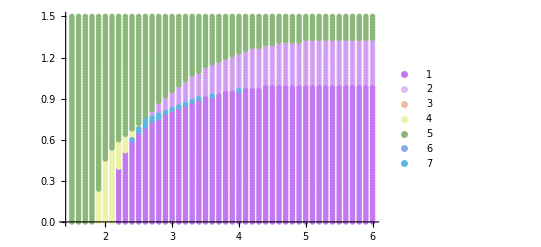

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[Join[Take[z2,{10,20}],{z2[[22]]},{z2[[26]]}]];
f3=Interpolation[Drop[z3,12]];
f4=Interpolation[Take[z4,{5,12}]];
```

```mathematica
z2
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{Null[5,1],Null[5,2]},{Null[6,1],Null[6,2]},{Null[7,1],Null[7,2]},{Null[8,1],Null[8,2]},{Null[9,1],Null[9,2]},{2.4,0.62},{2.5,0.7},{2.6,0.76},{2.7,0.78},{2.8,0.8},{2.9,0.82},{3.,0.84},{3.1,0.86},{3.2,0.88},{3.3,0.9},{3.4,0.92},{Null[21,1],Null[21,2]},{3.6,0.94},{Null[23,1],Null[23,2]},{Null[24,1],Null[24,2]},{Null[25,1],Null[25,2]},{4.,0.98},{Null[27,1],Null[27,2]},{Null[28,1],Null[28,2]},{Null[29,1],Null[29,2]},{Null[30,1],Null[30,2]},{Null[31,1],Null[31,2]},{Null[32,1],Null[32,2]},{Null[33,1],Null[33,2]},{Null[34,1],Null[34,2]},{Null[35,1],Null[35,2]},{Null[36,1],Null[36,2]},{Null[37,1],Null[37,2]},{Null[38,1],Null[38,2]},{Null[39,1],Null[39,2]},{Null[40,1],Null[40,2]},{Null[41,1],Null[41,2]},{Null[42,1],Null[42,2]},{Null[43,1],Null[43,2]},{Null[44,1],Null[44,2]},{Null[45,1],Null[45,2]},{Null[46,1],Null[46,2]}}

```mathematica
z3
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{Null[5,1],Null[5,2]},{Null[6,1],Null[6,2]},{Null[7,1],Null[7,2]},{Null[8,1],Null[8,2]},{Null[9,1],Null[9,2]},{Null[10,1],Null[10,2]},{Null[11,1],Null[11,2]},{Null[12,1],Null[12,2]},{2.7,0.82},{2.8,0.88},{2.9,0.92},{3.,0.96},{3.1,1.},{3.2,1.04},{3.3,1.08},{3.4,1.1},{3.5,1.14},{3.6,1.16},{3.7,1.18},{3.8,1.2},{3.9,1.22},{4.,1.24},{4.1,1.26},{4.2,1.28},{4.3,1.28},{4.4,1.3},{4.5,1.3},{4.6,1.32},{4.7,1.32},{4.8,1.32},{4.9,1.32},{5.,1.34},{5.1,1.34},{5.2,1.34},{5.3,1.34},{5.4,1.34},{5.5,1.34},{5.6,1.34},{5.7,1.34},{5.8,1.34},{5.9,1.34},{6.,1.34}}

```mathematica
z4
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{1.9,0.24},{2.,0.46},{2.1,0.54},{2.2,0.6},{2.3,0.64},{2.4,0.68},{2.5,0.72},{2.6,0.76},{Null[13,1],Null[13,2]},{Null[14,1],Null[14,2]},{Null[15,1],Null[15,2]},{Null[16,1],Null[16,2]},{Null[17,1],Null[17,2]},{Null[18,1],Null[18,2]},{Null[19,1],Null[19,2]},{Null[20,1],Null[20,2]},{Null[21,1],Null[21,2]},{Null[22,1],Null[22,2]},{Null[23,1],Null[23,2]},{Null[24,1],Null[24,2]},{Null[25,1],Null[25,2]},{Null[26,1],Null[26,2]},{Null[27,1],Null[27,2]},{Null[28,1],Null[28,2]},{Null[29,1],Null[29,2]},{Null[30,1],Null[30,2]},{Null[31,1],Null[31,2]},{Null[32,1],Null[32,2]},{Null[33,1],Null[33,2]},{Null[34,1],Null[34,2]},{Null[35,1],Null[35,2]},{Null[36,1],Null[36,2]},{Null[37,1],Null[37,2]},{Null[38,1],Null[38,2]},{Null[39,1],Null[39,2]},{Null[40,1],Null[40,2]},{Null[41,1],Null[41,2]},{Null[42,1],Null[42,2]},{Null[43,1],Null[43,2]},{Null[44,1],Null[44,2]},{Null[45,1],Null[45,2]},{Null[46,1],Null[46,2]}}

InterpolatingFunction::dmval: Input value {0.000139613} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.65} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

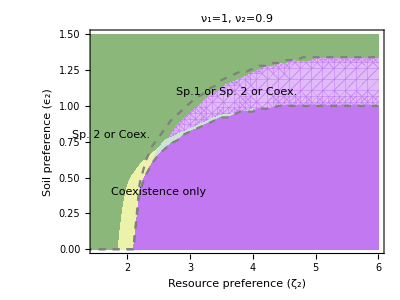

```mathematica
fig4d1=Show[{RegionPlot[{y<f4[x],y>f4[x]},{x,0,2.65},{y,0,1.5},PlotStyle->{{ColorData["Pastel",2/3],Opacity[1]},{ColorData[95,0]}},BoundaryStyle->None],RegionPlot[{y<f3[x]&&y>f1[x],y>f3[x]},{x,2.65,6},{y,0,1.5},PlotStyle->{{ColorData["Pastel",0],Opacity[0.5]},{ColorData[95,0]}},BoundaryStyle->None],RegionPlot[y<f2[x],{x,2.4,4},{y,0,1.5},PlotStyle->{ColorData["Pastel",0.8],Opacity[1]},BoundaryStyle->None],RegionPlot[y<f1[x],{x,1.5,6},{y,0,1.5},PlotStyle->{ColorData["Pastel",0],Opacity[1]},BoundaryStyle->None],ListLinePlot[{z1Sym,z2Sym},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotRange->{{1.5,6},Automatic},PlotLabel->Style["ν_1=1, ν_2=0.9",FontSize->18],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->18,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{1.4,1.4}],Inset[Text[Style["Sp. 2",FontSize->15]],{0.4,0.4}],Inset[Text[Style["Sp. 2 or Coex.",FontSize->13]],{1.75,0.8}],Inset[Text[Style["Sp.1 or Sp. 2 or Coex. ",FontSize->15]],{3.75,1.1}],Inset[Text[Style["Coexistence only ",FontSize->15]],{2.5,0.4}]}},AspectRatio->0.75]
```

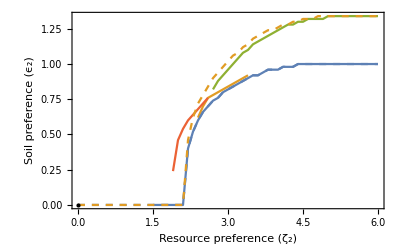

```mathematica
ListLinePlot[{z1,z2,z3,z4,z1Sym,z2Sym},PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3],ColorData[97,4],{ColorData[97,1],Dashed},{ColorData[97,2],Dashed}},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]}]
```

```mathematica
z1d=z1;
z2d=z2;
z3d=z3;
```

#### Intermediate asymmety ν_1=1, ν_2=0.7

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->0.7,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[1.5,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch20=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]];
If[Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]<0,Print[{j1,j2,eq[[j1,j2]],Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]}]]]];

If[Length[eq[[j1,j2]]]==1,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}];
If[Im[λ[[1]]]!=0,Print[{2,ζs[[j1]],ϵs[[j2]]}],
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}];
If[Im[λ[[1]]]!=0,Print[{3,ζs[[j1]],ϵs[[j2]]}],
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ3[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ1[[j1,j2]]<0&&λ2[[j1,j2]]>0&&λ3[[j1,j2]]<0&&ch1==1&&ch20==0,ch20=1];
If[λ2[[j1,j2]]<0&&ch20==1&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]>0&&λ3[[j1,j2]]<0&&ch20==1&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,
If[λ2[[j1,j2-1]]<0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]},z4[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1];ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{1,1.5,0.62}

{1,1.5,0.64}

{1,1.5,0.66}

{1,1.5,0.68}

{1,1.5,0.7}

{1,1.5,0.72}

{1,1.5,0.74}

{1,1.5,0.76}

{1,1.5,0.78}

{1,1.5,0.8}

{1,1.5,0.82}

{1,1.5,0.84}

{1,1.5,0.86}

{1,1.5,0.88}

{1,1.5,0.9}

{1,1.6,0.64}

{1,1.6,0.66}

{1,1.6,0.68}

{1,1.6,0.7}

{1,1.6,0.72}

{1,1.6,0.74}

{1,1.6,0.76}

{1,1.6,0.78}

{1,1.6,0.8}

{1,1.6,0.82}

{1,1.6,0.84}

{1,1.6,0.86}

{1,1.6,0.88}

{1,1.7,0.66}

{1,1.7,0.68}

{1,1.7,0.7}

{1,1.7,0.72}

{1,1.7,0.74}

{1,1.7,0.76}

{1,1.7,0.78}

{1,1.7,0.8}

{1,1.7,0.82}

{54.8125,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{299,2771,32,394,0,0}

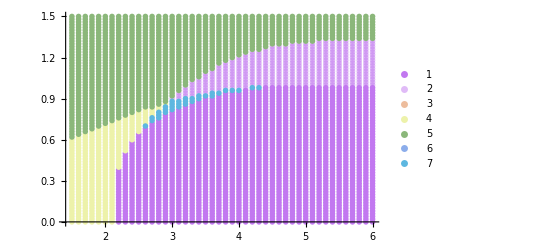

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[Join[Take[z2,{12,26}],Take[z2,{28,29}]]];
f3=Interpolation[Drop[z3,15]];
f4=Interpolation[Take[z4,15]];
```

```mathematica
z2
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{Null[5,1],Null[5,2]},{Null[6,1],Null[6,2]},{Null[7,1],Null[7,2]},{Null[8,1],Null[8,2]},{Null[9,1],Null[9,2]},{Null[10,1],Null[10,2]},{Null[11,1],Null[11,2]},{2.6,0.72},{2.7,0.78},{2.8,0.82},{2.9,0.86},{3.,0.9},{3.1,0.9},{3.2,0.92},{3.3,0.92},{3.4,0.94},{3.5,0.94},{3.6,0.96},{3.7,0.96},{3.8,0.98},{3.9,0.98},{4.,0.98},{Null[27,1],Null[27,2]},{4.2,1.},{4.3,1.},{Null[30,1],Null[30,2]},{Null[31,1],Null[31,2]},{Null[32,1],Null[32,2]},{Null[33,1],Null[33,2]},{Null[34,1],Null[34,2]},{Null[35,1],Null[35,2]},{Null[36,1],Null[36,2]},{Null[37,1],Null[37,2]},{Null[38,1],Null[38,2]},{Null[39,1],Null[39,2]},{Null[40,1],Null[40,2]},{Null[41,1],Null[41,2]},{Null[42,1],Null[42,2]},{Null[43,1],Null[43,2]},{Null[44,1],Null[44,2]},{Null[45,1],Null[45,2]},{Null[46,1],Null[46,2]}}

```mathematica
z3
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{Null[5,1],Null[5,2]},{Null[6,1],Null[6,2]},{Null[7,1],Null[7,2]},{Null[8,1],Null[8,2]},{Null[9,1],Null[9,2]},{Null[10,1],Null[10,2]},{Null[11,1],Null[11,2]},{Null[12,1],Null[12,2]},{Null[13,1],Null[13,2]},{Null[14,1],Null[14,2]},{Null[15,1],Null[15,2]},{3.,0.92},{3.1,0.96},{3.2,1.},{3.3,1.04},{3.4,1.06},{3.5,1.1},{3.6,1.12},{3.7,1.16},{3.8,1.18},{3.9,1.2},{4.,1.22},{4.1,1.24},{4.2,1.26},{4.3,1.26},{4.4,1.28},{4.5,1.3},{4.6,1.3},{4.7,1.3},{4.8,1.32},{4.9,1.32},{5.,1.32},{5.1,1.32},{5.2,1.34},{5.3,1.34},{5.4,1.34},{5.5,1.34},{5.6,1.34},{5.7,1.34},{5.8,1.34},{5.9,1.34},{6.,1.34}}

```mathematica
z4
```

{{1.5,0.62},{1.6,0.64},{1.7,0.66},{1.8,0.68},{1.9,0.7},{2.,0.72},{2.1,0.74},{2.2,0.76},{2.3,0.78},{2.4,0.8},{2.5,0.82},{2.6,0.84},{2.7,0.84},{2.8,0.86},{2.9,0.88},{Null[16,1],Null[16,2]},{Null[17,1],Null[17,2]},{Null[18,1],Null[18,2]},{Null[19,1],Null[19,2]},{Null[20,1],Null[20,2]},{Null[21,1],Null[21,2]},{Null[22,1],Null[22,2]},{Null[23,1],Null[23,2]},{Null[24,1],Null[24,2]},{Null[25,1],Null[25,2]},{Null[26,1],Null[26,2]},{Null[27,1],Null[27,2]},{Null[28,1],Null[28,2]},{Null[29,1],Null[29,2]},{Null[30,1],Null[30,2]},{Null[31,1],Null[31,2]},{Null[32,1],Null[32,2]},{Null[33,1],Null[33,2]},{Null[34,1],Null[34,2]},{Null[35,1],Null[35,2]},{Null[36,1],Null[36,2]},{Null[37,1],Null[37,2]},{Null[38,1],Null[38,2]},{Null[39,1],Null[39,2]},{Null[40,1],Null[40,2]},{Null[41,1],Null[41,2]},{Null[42,1],Null[42,2]},{Null[43,1],Null[43,2]},{Null[44,1],Null[44,2]},{Null[45,1],Null[45,2]},{Null[46,1],Null[46,2]}}

InterpolatingFunction::dmval: Input value {2.95} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.91184} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

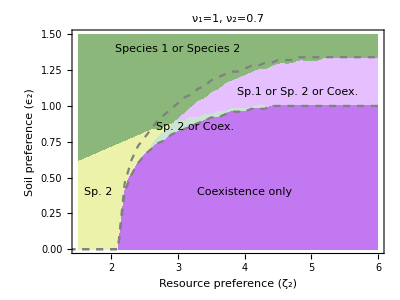

```mathematica
fig4d2=Show[{RegionPlot[{y<f4[x],y>f4[x]},{x,1.5,2.95},{y,0,1.5},PlotStyle->{{ColorData["Pastel",2/3],Opacity[1]},{ColorData[95,0],Opacity[1]}},BoundaryStyle->None],RegionPlot[{y<f3[x]&&y>f1[x],y>f3[x]},{x,2.95,6},{y,0,1.5},PlotStyle->{{RGBColor[0.9,0.75,1,0.99]},{ColorData[95,0],Opacity[1]}},BoundaryStyle->None],RegionPlot[y<f2[x],{x,2.6,4.3},{y,0,1.5},PlotStyle->{ColorData["Pastel",0.8],Opacity[1]},BoundaryStyle->None],RegionPlot[y<f1[x],{x,1.5,6},{y,0,1.5},PlotStyle->{ColorData["Pastel",0],Opacity[1]},BoundaryStyle->None],ListLinePlot[{z1Sym,z2Sym},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotRange->{{1.5,6},Automatic},PlotLabel->Style["ν_1=1, ν_2=0.7",FontSize->18],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->18,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{3,1.4}],Inset[Text[Style["Sp. 2",FontSize->15]],{1.8,0.4}],Inset[Text[Style["Sp. 2 or Coex.",FontSize->13]],{3.25,0.85}],Inset[Text[Style["Sp.1 or Sp. 2 or Coex. ",FontSize->15]],{4.8,1.1}],Inset[Text[Style["Coexistence only ",FontSize->15]],{4,0.4}]}},AspectRatio->0.75]
```

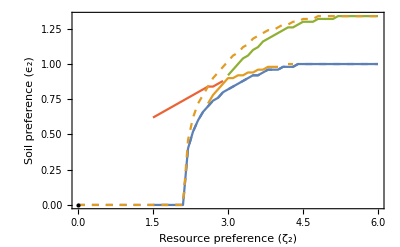

```mathematica
ListLinePlot[{z1,z2,z3,z4,z1Sym,z2Sym},PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3],ColorData[97,4],{ColorData[97,1],Dashed},{ColorData[97,2],Dashed}},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]}]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4d.pdf",fig4d2];
```

#### Intense asymmety ν_1=1, ν_2=0.5

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->0.5,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[1.5,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch20=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]];
If[Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]<0,Print[{j1,j2,eq[[j1,j2]],Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]}]]]];

If[Length[eq[[j1,j2]]]==1,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]];
If[Im[λ[[1]]]!=0,Print[{1,ζs[[j1]],ϵs[[j2]]}],
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}];
If[Im[λ[[1]]]!=0,Print[{2,ζs[[j1]],ϵs[[j2]]}],
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}];
If[Im[λ[[1]]]!=0,Print[{3,ζs[[j1]],ϵs[[j2]]}],
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ3[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ1[[j1,j2]]<0&&λ2[[j1,j2]]>0&&λ3[[j1,j2]]<0&&ch1==1&&ch20==0,ch20=1];
If[λ2[[j1,j2]]<0&&ch20==1&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]>0&&λ3[[j1,j2]]<0&&ch20==1&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,
If[λ2[[j1,j2-1]]<0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]},z4[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1];ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{54.7344,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{383,2711,37,365,0,0}

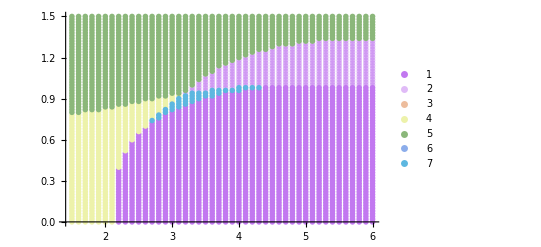

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[Take[z2,{13,29}]];
f3=Interpolation[Drop[z3,17]];
f4=Interpolation[Take[z4,17]];
```

```mathematica
z2
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{Null[5,1],Null[5,2]},{Null[6,1],Null[6,2]},{Null[7,1],Null[7,2]},{Null[8,1],Null[8,2]},{Null[9,1],Null[9,2]},{Null[10,1],Null[10,2]},{Null[11,1],Null[11,2]},{Null[12,1],Null[12,2]},{2.7,0.76},{2.8,0.8},{2.9,0.84},{3.,0.88},{3.1,0.92},{3.2,0.94},{3.3,0.96},{3.4,0.96},{3.5,0.96},{3.6,0.98},{3.7,0.98},{3.8,0.98},{3.9,0.98},{4.,1.},{4.1,1.},{4.2,1.},{4.3,1.},{Null[30,1],Null[30,2]},{Null[31,1],Null[31,2]},{Null[32,1],Null[32,2]},{Null[33,1],Null[33,2]},{Null[34,1],Null[34,2]},{Null[35,1],Null[35,2]},{Null[36,1],Null[36,2]},{Null[37,1],Null[37,2]},{Null[38,1],Null[38,2]},{Null[39,1],Null[39,2]},{Null[40,1],Null[40,2]},{Null[41,1],Null[41,2]},{Null[42,1],Null[42,2]},{Null[43,1],Null[43,2]},{Null[44,1],Null[44,2]},{Null[45,1],Null[45,2]},{Null[46,1],Null[46,2]}}

```mathematica
z3
```

{{Null[1,1],Null[1,2]},{Null[2,1],Null[2,2]},{Null[3,1],Null[3,2]},{Null[4,1],Null[4,2]},{Null[5,1],Null[5,2]},{Null[6,1],Null[6,2]},{Null[7,1],Null[7,2]},{Null[8,1],Null[8,2]},{Null[9,1],Null[9,2]},{Null[10,1],Null[10,2]},{Null[11,1],Null[11,2]},{Null[12,1],Null[12,2]},{Null[13,1],Null[13,2]},{Null[14,1],Null[14,2]},{Null[15,1],Null[15,2]},{Null[16,1],Null[16,2]},{Null[17,1],Null[17,2]},{3.2,0.96},{3.3,1.},{3.4,1.04},{3.5,1.08},{3.6,1.1},{3.7,1.14},{3.8,1.16},{3.9,1.18},{4.,1.2},{4.1,1.22},{4.2,1.24},{4.3,1.26},{4.4,1.26},{4.5,1.28},{4.6,1.3},{4.7,1.3},{4.8,1.3},{4.9,1.32},{5.,1.32},{5.1,1.32},{5.2,1.34},{5.3,1.34},{5.4,1.34},{5.5,1.34},{5.6,1.34},{5.7,1.34},{5.8,1.34},{5.9,1.34},{6.,1.34}}

```mathematica
z4
```

{{1.5,0.8},{1.6,0.8},{1.7,0.82},{1.8,0.82},{1.9,0.82},{2.,0.84},{2.1,0.84},{2.2,0.86},{2.3,0.86},{2.4,0.88},{2.5,0.88},{2.6,0.9},{2.7,0.9},{2.8,0.92},{2.9,0.92},{3.,0.94},{3.1,0.94},{Null[18,1],Null[18,2]},{Null[19,1],Null[19,2]},{Null[20,1],Null[20,2]},{Null[21,1],Null[21,2]},{Null[22,1],Null[22,2]},{Null[23,1],Null[23,2]},{Null[24,1],Null[24,2]},{Null[25,1],Null[25,2]},{Null[26,1],Null[26,2]},{Null[27,1],Null[27,2]},{Null[28,1],Null[28,2]},{Null[29,1],Null[29,2]},{Null[30,1],Null[30,2]},{Null[31,1],Null[31,2]},{Null[32,1],Null[32,2]},{Null[33,1],Null[33,2]},{Null[34,1],Null[34,2]},{Null[35,1],Null[35,2]},{Null[36,1],Null[36,2]},{Null[37,1],Null[37,2]},{Null[38,1],Null[38,2]},{Null[39,1],Null[39,2]},{Null[40,1],Null[40,2]},{Null[41,1],Null[41,2]},{Null[42,1],Null[42,2]},{Null[43,1],Null[43,2]},{Null[44,1],Null[44,2]},{Null[45,1],Null[45,2]},{Null[46,1],Null[46,2]}}

InterpolatingFunction::dmval: Input value {3.15} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.10658} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

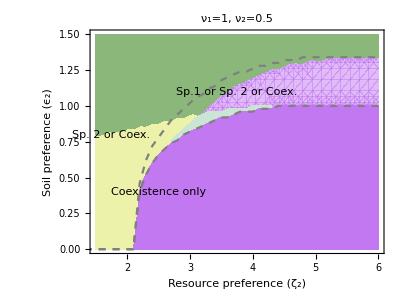

```mathematica
fig4d3=Show[{RegionPlot[{y<f4[x],y>f4[x]},{x,1.5,3.15},{y,0,1.5},PlotStyle->{{ColorData["Pastel",2/3],Opacity[1]},{ColorData[95,0]}},BoundaryStyle->None],RegionPlot[{y<f3[x]&&y>f1[x],y>f3[x]},{x,3.15,6},{y,0,1.5},PlotStyle->{{ColorData["Pastel",0],Opacity[0.5]},{ColorData[95,0]}},BoundaryStyle->None],RegionPlot[y<f2[x],{x,2.7,4.3},{y,0,1.5},PlotStyle->{ColorData["Pastel",0.8],Opacity[1]},BoundaryStyle->None],RegionPlot[y<f1[x],{x,1.5,6},{y,0,1.5},PlotStyle->{ColorData["Pastel",0],Opacity[1]},BoundaryStyle->None],ListLinePlot[{z1Sym,z2Sym},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotRange->{{1.5,6},Automatic},PlotLabel->Style["ν_1=1, ν_2=0.5",FontSize->18],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->18,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{1.4,1.4}],Inset[Text[Style["Sp. 2",FontSize->15]],{0.4,0.4}],Inset[Text[Style["Sp. 2 or Coex.",FontSize->13]],{1.75,0.8}],Inset[Text[Style["Sp.1 or Sp. 2 or Coex. ",FontSize->15]],{3.75,1.1}],Inset[Text[Style["Coexistence only ",FontSize->15]],{2.5,0.4}]}},AspectRatio->0.75]
```

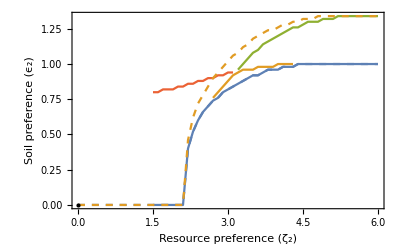

```mathematica
ListLinePlot[{z1,z2,z3,z4,z1Sym,z2Sym},PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3],ColorData[97,4],{ColorData[97,1],Dashed},{ColorData[97,2],Dashed}},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]}]
```

#### Summary

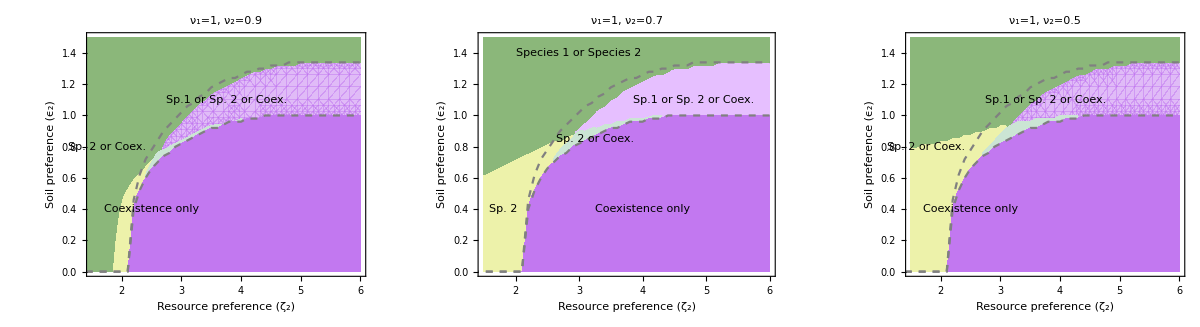

```mathematica
GraphicsRow[{fig4d1,fig4d2,fig4d3},ImageSize->1200]
```

## Supplement for Figure 4 (Invasibility)

### No PSF

#### Calculation

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->0,Subscript[η, 2]->0};
ϵs=Range[0,1.5,0.05];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf","α","α_12","α_21"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
Do[
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

#### Result

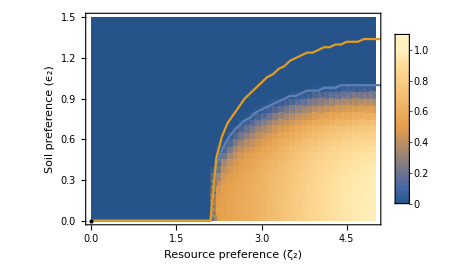

```mathematica
figA5a=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1Sym,z2Sym}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

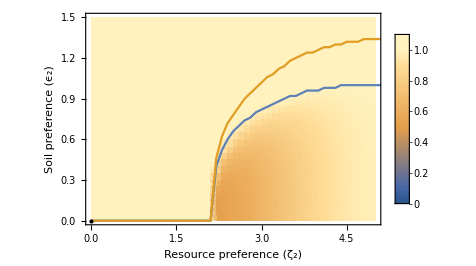

```mathematica
figA5b=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1Sym,z2Sym}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA5a.pdf",figA5a];
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA5b.pdf",figA5b];
```

### Symmetric invader

#### Calculation

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.01];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Do[
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

#### Result

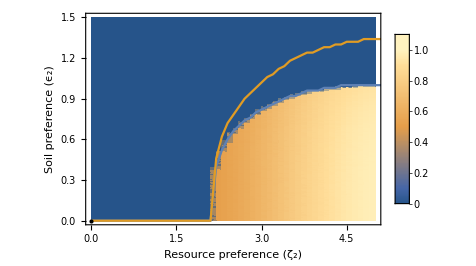

```mathematica
figA6a=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1Sym,z2Sym}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

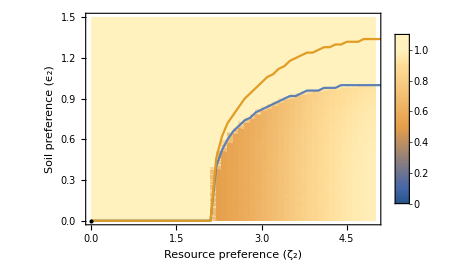

```mathematica
figA6b=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1Sym,z2Sym}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA6a.pdf",figA6a];
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA6b.pdf",figA6b];
```

### Strongly conditioning invader

#### Calculation

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1.2};
ϵs=Range[0,1.5,0.01];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Do[
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

$Aborted

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

#### Result

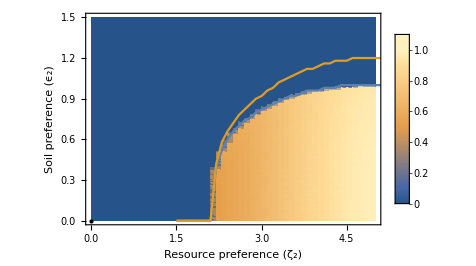

```mathematica
figA7a=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1a,z2a}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

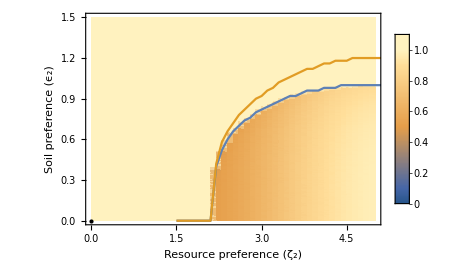

```mathematica
figA7b=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1a,z2a}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA7a.pdf",figA7a];
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA7b.pdf",figA7b];
```

### Soil tolerant invader

#### Calculation

```mathematica
pars={Subscript[ω, 1]->1.1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.01];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=1000;
```

This defines Dormand and Prince coefficients to solve ODE equivalently to ode45 in MATLAB

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
Do[
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

#### Result

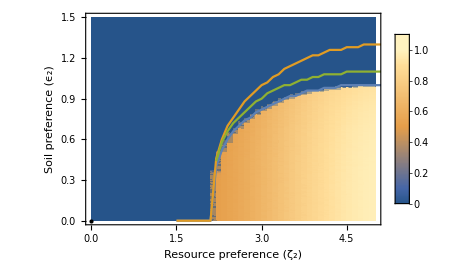

```mathematica
figA8a=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1b,z3b,z2b}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

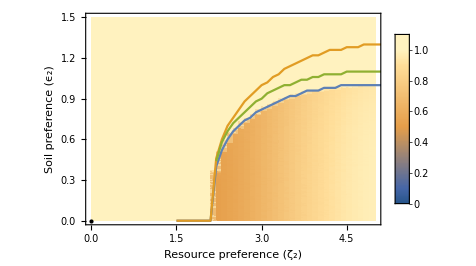

```mathematica
figA8b=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1b,z3b,z2b}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA8a.pdf",figA8a];
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA8b.pdf",figA8b];
```

### Strongly competing invader

#### Calculation

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1.2,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.01];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Do[
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

#### Result

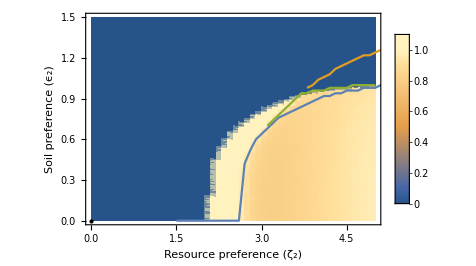

```mathematica
figA9a=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1c,z3c,z2c}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

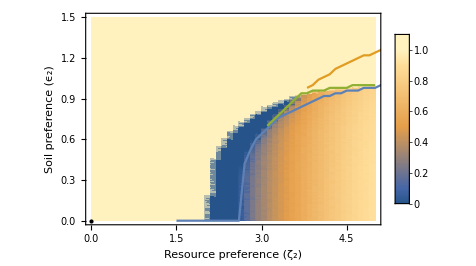

```mathematica
figA9b=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1c,z3c,z2c}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA9a.pdf",figA9a];
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA9b.pdf",figA9b];
```

### Competitively insensitive invader

#### Calculation

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->0.9,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.01];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Do[
Do[
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,ζs[[j1]],0];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

#### Result

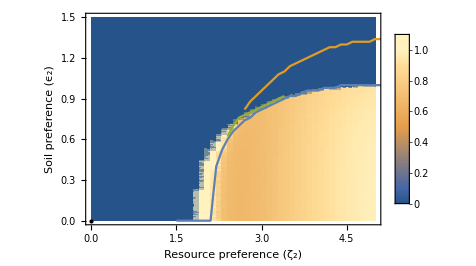

```mathematica
figA10a=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1d,z3d,z2d}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

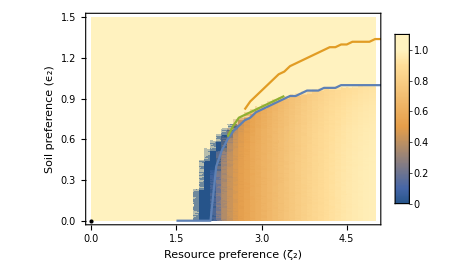

```mathematica
figA10b=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1d,z3d,z2d}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA10a.pdf",figA10a];
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA10b.pdf",figA10b];
```

## Numerics

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->0,Subscript[η, 2]->0,ϵ->0.2,ζ->3};
```

```mathematica
x0=1;y0=0.0001;z0=0; T=100; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

```mathematica
nsol=NDSolve[{D[x[t],t]==dx,D[y[t],t]==dy,D[z[t],t]==dz,x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
```

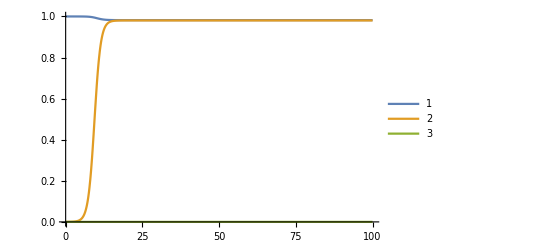

```mathematica
Plot[{x[t]/.nsol,y[t]/.nsol,z[t]/.nsol},{t,0,100},PlotRange->{0,1},PlotLegends->Automatic]
```